```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/andrei/Work/physics/B-physics/BcBcNLO/calc/BcBc/PV/west/gamma/renorm

```mathematica
PrependTo[$Path,"/home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg"];
```

```mathematica
<<X`
```

Package-X v1.0.4, by Hiren H. Patel

For more information, see the

```mathematica
NumericQ[r]=True;
```

```mathematica
PackageXSubs={LDot[p3,p3]->m^2,LDot[p4,p4]->m^2,LDot[p3,p4]->s/2-m^2,mc-> r m, mb-> (1-r) m};
```

```mathematica
toABC={pvA[a_,b_]:>A[b],pvB[a_,b_,c___]:>B[c],pvC[a_,b_,c_,d___]:>C[d],pvC0[a__]:>C[a]};
topvABC={A[a_]:>pvA[0,a],B[a__]:>pvB[0,0,a],C[a__]:>pvC[0,0,0,a]};
```

```mathematica
factor=(Exp[EulerGamma] 1/(4 Pi))^-eps
```

ⅇ^(ℽ (-eps)) (4 π)^eps

```mathematica
ff=Gamma[1-2 eps]/(Gamma[1-eps]^2 Gamma[1+eps](4 Pi)^eps I/(16 Pi^2))
```

-(ⅈ (4 π)^(2-eps) 1-2 eps)/((1-eps)^2 eps+1)

```mathematica
invff=1/ff
```

(ⅈ (4 π)^(eps-2) (1-eps)^2 eps+1)/(1-2 eps)

```mathematica
Normal[Series[FullSimplify[1/factor invff],{eps,0,1}]]
```

ⅈ/(16 π^2)

```mathematica
norm=Expand[Normal[Series[FullSimplify[1/factor invff],{eps,0,2}]]/(I/(16 Pi^2))]
```

1-(π^2 eps^2)/12

```mathematica
Fb=(((1-r)^2 m^2)/mmu)^-eps
```

((m^2 (1-r)^2)/mmu)^-eps

```mathematica
Fc=((r^2 m^2)/mmu)^-eps
```

((m^2 r^2)/mmu)^-eps

```mathematica
Fb=Plus@@ Factor[List@@ Normal[Series[Fb,{eps,0,1}]]/.{Log[(m^2 (1-r)^2)/mmu]->Log[m^2/mmu]+ 2 Log[1-r]}]
```

1-eps (log(m^2/mmu)+2 log(1-r))

```mathematica
Fc=Plus@@ Factor[List@@ Normal[Series[Fc,{eps,0,1}]]/.{Log[(m^2 r^2)/mmu]->Log[m^2/mmu]+ 2 Log[r]}]
```

1-eps (log(m^2/mmu)+2 log(r))

```mathematica
A0[m_]:=m^2+m^2/eps+eps*m^2+(eps*m^2*Pi^2)/6+m^2*Log[mmu/m^2]+eps*m^2*Log[mmu/m^2]+(eps*m^2*Log[mmu/m^2]^2)/2
```

```mathematica
F21[z_]:=(1-eps)/(2 (1-2 eps) z)(1+z-(1-z)^(1-2 eps)-2 (1-z)^(1-2 eps) eps (eps PolyLog[1,1,z]+Hui eps^2 Sum[(-2)^(j-k) PolyLog[k,3-k],{k,1,2}]))
```

```mathematica
B0polylog[s_,m1_,m2_]:=Block[{x,y,lam},If[m1≠ 0 && m2≠0,x=m1^2/s;y=m2^2/s;lam=√((1-x-y)^2-4 x y);  mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps ((Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps] lam^(1- 2 eps)-Gamma[-1+eps] 1/2(1+x-y-lam) (-x)^-eps F21[(1+x-y-lam)^2/(4 x)]-
Gamma[-1+eps] 1/2(1-x+y-lam) (-y)^-eps F21[(1-x+y-lam)^2/(4 y)]),If[m1==0 && m2 ≠ 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m2^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m2^2],If[m1≠ 0 && m2== 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m1^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m1^2],If[m1==0 && m2==0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps (Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps]]]]]]
```

```mathematica
<<renormAmpWest.res
```

```mathematica
<<renormAmpSquaredCheckWest.res
```

```mathematica
(* X[a_]:=norm *)
```

```mathematica
X[a_]:=1
```

```mathematica
A1=Coefficient[renormAmp,AA[1]];
```

```mathematica
A1B1=Coefficient[matrixelement,AA[1] BB[1]];
```

```mathematica
mc=1.5;mb=4.9;m=mc+mb;r=mc/m;CF=4/3;CA=3;pi=Pi;s=15^2;mt=175;AL=1/137;nf=6;
```

```mathematica
(2mc+2 mc)^2
```

36.

```mathematica
(* AS=0.3; mmu=(2 m)^2; *)
```

```mathematica
ex[1]=Collect[Expand[A1//N],{A[___],B[___],C[___]}]
```

0.0000269814 log(0.234375) AS^2+0.0000418567 log(0.765625) AS^2-0.0000344191 log(0.0244141 mmu) AS^2-(0.0000578977 AS^2)/eps-0.0000458921 AS^2+0.0000421487 AS+(-7.83043×10^-6 eps AS^2-(2.93679×10^-7 AS^2)/eps+9.94479×10^-6 AS^2) A(1.5)+(-8.28255×10^-7 eps AS^2+(8.99017×10^-8 AS^2)/eps+6.00113×10^-6 AS^2) A(4.9)+(3.81793×10^-7 AS^2-1.27264×10^-7 AS^2 eps) A(175.)+(0.000106452 AS^2-0.000108933 AS^2 eps) B(12.3596,0.,0.)+(2.59062×10^-7 eps AS^2+(2.61556×10^-6 AS^2)/eps-7.58918×10^-6 AS^2) B(12.3596,1.5,1.5)+(-5.55862×10^-6 eps AS^2-0.0000147807 AS^2) B(12.3596,4.9,4.9)+(-0.00783628 eps AS^2-0.011758 AS^2) B(12.3596,175.,175.)+(-7.1157×10^-7 eps AS^2-(3.36444×10^-6 AS^2)/eps+8.77627×10^-6 AS^2) B(51.9348,1.5,4.9)+(-8.54396×10^-6 eps AS^2-(3.36444×10^-6 AS^2)/eps+5.01136×10^-6 AS^2) B(51.9348,4.9,1.5)+(0.0000609759 eps AS^2+0.0000500049 AS^2) B(76.7444,0.,4.9)+(0.000127293 AS^2 eps-0.000207865 AS^2) B(76.7444,4.9,0.)+(0.0000111488 AS^2-0.0000999427 AS^2 eps) B(131.891,0.,0.)+(4.14098×10^-6 AS^2-2.16072×10^-6 AS^2 eps) B(131.891,1.5,1.5)+(1.63727×10^-7 eps AS^2+(2.61556×10^-6 AS^2)/eps+1.2051×10^-6 AS^2) B(131.891,4.9,4.9)+(0.0000420913 eps AS^2+0.000063341 AS^2) B(131.891,175.,175.)+(0.000193872 AS^2 eps-0.0000569264 AS^2) B(174.516,0.,1.5)+(0.0000304024 AS^2 eps-3.39444×10^-6 AS^2) B(174.516,1.5,0.)+(0.00004577 AS^2-0.000121724 AS^2 eps) B(225.,1.5,1.5)+(0.0000291507 AS^2 eps-0.0000467851 AS^2) B(225.,4.9,4.9)+(0.000176523 AS^2 eps-0.0000313027 AS^2) C[2.25,12.3596,2.25,0,1.5,0]+(0.000633467 AS^2-0.000703608 AS^2 eps) C[2.25,76.7444,40.96,4.9,1.5,0]+(-0.0000324365 eps AS^2-0.0000249407 AS^2) C[2.25,76.7444,51.9348,4.9,1.5,0]+(0.000611945 AS^2 eps-0.0000683187 AS^2) C[2.25,131.891,174.516,0,1.5,0]+(-0.000097918 eps AS^2-0.000092864 AS^2) C[2.25,174.516,131.891,1.5,1.5,0]+(0.000695193 AS^2-0.00207667 AS^2 eps) C[2.25,174.516,225,1.5,1.5,0]+(0.00131716 AS^2 eps-0.00171698 AS^2) C[24.01,12.3596,76.7444,0,4.9,0]+(0.000181832 eps AS^2+0.000183163 AS^2) C[24.01,76.7444,12.3596,4.9,4.9,0]+(-0.00103674 eps AS^2-0.00151027 AS^2) C[24.01,76.7444,225,4.9,4.9,0]+(0.000773502 AS^2 eps-0.00148435 AS^2) C[24.01,131.891,24.01,0,4.9,0]+(0.00166298 AS^2-0.00166752 AS^2 eps) C[24.01,174.516,40.96,1.5,4.9,0]+(0.000330099 eps AS^2+0.0000119178 AS^2) C[24.01,174.516,51.9348,1.5,4.9,0]+(-0.000268842 eps AS^2-9.41547×10^-6 AS^2) C[51.9348,51.9348,225,1.5,1.5,4.9]+(0.0000851969 AS^2 eps-7.15811×10^-6 AS^2) C[76.7444,2.25,51.9348,1.5,4.9,0]+(0.00170642 AS^2 eps-0.0006562 AS^2) C[76.7444,12.3596,24.01,0,4.9,0]+(0.0000641646 AS^2-0.000206436 AS^2 eps) C[76.7444,24.01,12.3596,4.9,4.9,0]+(0.00238029 eps AS^2+0.000228177 AS^2) C[76.7444,24.01,225,4.9,4.9,0]+(0.000166368 AS^2 eps-6.72231×10^-6 AS^2) C[174.516,2.25,131.891,1.5,1.5,0]+(0.00028465 eps AS^2+0.0000143162 AS^2) C[174.516,24.01,51.9348,4.9,1.5,0]+(0.00120521 AS^2 eps-0.000432652 AS^2) C[174.516,131.891,2.25,0,1.5,0]+(-0.0000891172 eps AS^2-0.0000280248 AS^2) C[225,51.9348,51.9348,1.5,4.9,4.9]

```mathematica
B[14,0.,0.]/.{B[s_,0.,0.]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]}
```

0.5 eps (-(1.27811-6.28319 ⅈ) log(mmu)-(5.46121+4.01532 ⅈ)+1. log^2(mmu))-(0.639057-3.14159 ⅈ)+1/eps+log(mmu)

```mathematica
ex[2]=Normal[Series[ex[1]/.{A[m_]:> A0[m],B[s_,0.,0.]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]],B[s_,m_,0.]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]],B[s_,0.,m_]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]],B[s_,m1_,m2_]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]],log[a_]:>  Log[a]},{eps,0,1}]]
```

eps (0.000176523 AS^2 C[2.25,12.3596,2.25,0,1.5,0]-0.000703608 AS^2 C[2.25,76.7444,40.96,4.9,1.5,0]-0.0000324365 AS^2 C[2.25,76.7444,51.9348,4.9,1.5,0]+0.000611945 AS^2 C[2.25,131.891,174.516,0,1.5,0]-0.000097918 AS^2 C[2.25,174.516,131.891,1.5,1.5,0]-0.00207667 AS^2 C[2.25,174.516,225,1.5,1.5,0]+0.00131716 AS^2 C[24.01,12.3596,76.7444,0,4.9,0]+0.000181832 AS^2 C[24.01,76.7444,12.3596,4.9,4.9,0]-0.00103674 AS^2 C[24.01,76.7444,225,4.9,4.9,0]+0.000773502 AS^2 C[24.01,131.891,24.01,0,4.9,0]-0.00166752 AS^2 C[24.01,174.516,40.96,1.5,4.9,0]+0.000330099 AS^2 C[24.01,174.516,51.9348,1.5,4.9,0]-0.000268842 AS^2 C[51.9348,51.9348,225,1.5,1.5,4.9]+0.0000851969 AS^2 C[76.7444,2.25,51.9348,1.5,4.9,0]+0.00170642 AS^2 C[76.7444,12.3596,24.01,0,4.9,0]-0.000206436 AS^2 C[76.7444,24.01,12.3596,4.9,4.9,0]+0.00238029 AS^2 C[76.7444,24.01,225,4.9,4.9,0]+0.000166368 AS^2 C[174.516,2.25,131.891,1.5,1.5,0]+0.00028465 AS^2 C[174.516,24.01,51.9348,4.9,1.5,0]+0.00120521 AS^2 C[174.516,131.891,2.25,0,1.5,0]-0.0000891172 AS^2 C[225,51.9348,51.9348,1.5,4.9,4.9]-(0.00589974+1.67092×10^-16 ⅈ) AS^2 log^2(mmu)+(0.11346-0.000109114 ⅈ) AS^2 log(mmu)-(0.535986-0.00077014 ⅈ) AS^2+0.0058462 AS^2 log^2(0.0000326531 mmu)+0.0000720436 AS^2 log^2(0.0416493 mmu)+0.0000111879 AS^2 log^2(0.444444 mmu)+0.00779494 AS^2 log(0.0000326531 mmu)+0.000124201 AS^2 log(0.0416493 mmu)+4.75731×10^-6 AS^2 log(0.444444 mmu))-0.0000313027 AS^2 C[2.25,12.3596,2.25,0,1.5,0]+0.000633467 AS^2 C[2.25,76.7444,40.96,4.9,1.5,0]-0.0000249407 AS^2 C[2.25,76.7444,51.9348,4.9,1.5,0]-0.0000683187 AS^2 C[2.25,131.891,174.516,0,1.5,0]-0.000092864 AS^2 C[2.25,174.516,131.891,1.5,1.5,0]+0.000695193 AS^2 C[2.25,174.516,225,1.5,1.5,0]-0.00171698 AS^2 C[24.01,12.3596,76.7444,0,4.9,0]+0.000183163 AS^2 C[24.01,76.7444,12.3596,4.9,4.9,0]-0.00151027 AS^2 C[24.01,76.7444,225,4.9,4.9,0]-0.00148435 AS^2 C[24.01,131.891,24.01,0,4.9,0]+0.00166298 AS^2 C[24.01,174.516,40.96,1.5,4.9,0]+0.0000119178 AS^2 C[24.01,174.516,51.9348,1.5,4.9,0]-9.41547×10^-6 AS^2 C[51.9348,51.9348,225,1.5,1.5,4.9]-7.15811×10^-6 AS^2 C[76.7444,2.25,51.9348,1.5,4.9,0]-0.0006562 AS^2 C[76.7444,12.3596,24.01,0,4.9,0]+0.0000641646 AS^2 C[76.7444,24.01,12.3596,4.9,4.9,0]+0.000228177 AS^2 C[76.7444,24.01,225,4.9,4.9,0]-6.72231×10^-6 AS^2 C[174.516,2.25,131.891,1.5,1.5,0]+0.0000143162 AS^2 C[174.516,24.01,51.9348,4.9,1.5,0]-0.000432652 AS^2 C[174.516,131.891,2.25,0,1.5,0]-0.0000280248 AS^2 C[225,51.9348,51.9348,1.5,4.9,4.9]-(0.0117961+2.64464×10^-15 ⅈ) AS^2 log(mmu)+(0.121287-0.000111271 ⅈ) AS^2+((3.81165×10^-21-3.04248×10^-31 ⅈ) AS^2)/eps^2+1/eps(2.15854×10^-6 AS^2 log(0.0416493 mmu)-6.60777×10^-7 AS^2 log(0.444444 mmu)-(1.49776×10^-6+3.04248×10^-31 ⅈ) AS^2 log(mmu)+(6.32501×10^-6-2.64464×10^-15 ⅈ) AS^2)+1.07927×10^-6 AS^2 log^2(0.0416493 mmu)-3.30389×10^-7 AS^2 log^2(0.444444 mmu)-(7.48881×10^-7+1.52124×10^-31 ⅈ) AS^2 log^2(mmu)+0.0116924 AS^2 log(0.0000326531 mmu)-0.0000344191 AS^2 log(0.0244141 mmu)+0.000146246 AS^2 log(0.0416493 mmu)+0.000021715 AS^2 log(0.444444 mmu)+0.0000421487 AS

```mathematica
(* ex[3]=LoopRefine[N[(Chop[ex[1]]/.{C[___]-> 0,B[s_,m1_,m2_]-> B[s+0.000000000000001*I,m1,m2],log[a_]:>  Log[a]})/.topvABC]]/.{ϵ-> eps,μR^2-> mmu} *)
```

```mathematica
ex[3]=LoopRefine[ex[2]/.topvABC]
```

1/eps AS^2 ((0.11346-0.000109114 ⅈ) eps^2-(0.0117961+2.64464×10^-15 ⅈ) eps-(1.49776×10^-6+0. ⅈ)) log(mmu)+1/eps^2 AS (AS ((0.121082+0.0000486261 ⅈ) eps^2+(-0.535692+0.000477948 ⅈ) eps^3+(6.32501×10^-6-2.64464×10^-15 ⅈ) eps+(3.81165×10^-21-3.04248×10^-31 ⅈ))+(0.0000421487-1.32349×10^-23 ⅈ) eps^2)+(AS^2 (0.000124201 eps^2+0.000146246 eps+2.15854×10^-6) log(0.0416493 mmu))/eps+(AS^2 (4.75731×10^-6 eps^2+0.000021715 eps-6.60777×10^-7) log(0.444444 mmu))/eps+0.0058462 AS^2 eps log^2(0.0000326531 mmu)+AS^2 (0.0000720436 eps+1.07927×10^-6) log^2(0.0416493 mmu)+AS^2 (0.0000111879 eps-3.30389×10^-7) log^2(0.444444 mmu)+AS^2 ((-0.00589974-1.67092×10^-16 ⅈ) eps-(7.48881×10^-7+1.52124×10^-31 ⅈ)) log^2(mmu)+AS^2 (0.00779494 eps+0.0116924) log(0.0000326531 mmu)-0.0000344191 AS^2 log(0.0244141 mmu)

```mathematica
ex[4]=Chop[Normal[Series[FullSimplify[ex[3]],{eps,0,0}]]]
```

-(0.0000395596-0.0000486261 ⅈ) AS^2+0.0000234786 AS^2 log(mmu)+0.0000421487 AS

```mathematica
ex[5]=Collect[Chop[ex[4]],AS]/.{AS-> z *0.3}//Expand
```

2.11308×10^-6 z^2 log(mmu)-(3.56036×10^-6-4.37635×10^-6 ⅈ) z^2+0.0000126446 z

```mathematica
ex[6]=Normal[Series[(Conjugate[ex[5]] ex[5])/.{Conjugate[z]-> z,Conjugate[Log[mmu]]-> Log[mmu]},{z,0,3}]]
```

z^3 (5.34381×10^-11 log(mmu)-9.00388×10^-11)+1.59886×10^-10 z^2

```mathematica
ratioAmp[mu2_]:=Abs[N[Coefficient[ex[5],z^2]/Coefficient[ex[5],z]/.{mmu-> mu2}]]
```

```mathematica
ratioAmpSquare[mu2_]:=Abs[N[Coefficient[ex[6],z^3]/Coefficient[ex[6],z^2]/.{mmu-> mu2}]]
```

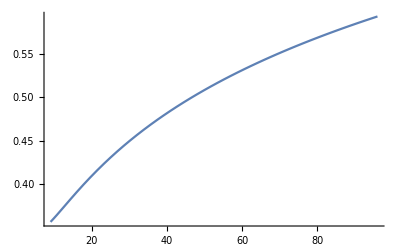

```mathematica
Plot[ratioAmp[mmu],{mmu,(2mc)^2,(2mb)^2}]
```

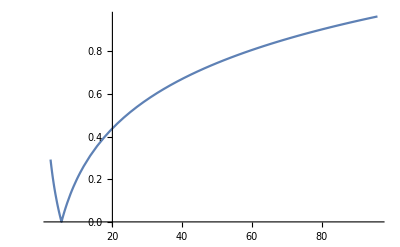

```mathematica
Plot[ratioAmpSquare[mmu],{mmu,(mc)^2,(2mb)^2}]
```

```mathematica
ratioAmp[m^2]
```

0.484363

```mathematica
ratioAmp[(2mc)^2]
```

0.356535

```mathematica
ratioAmp[(mc)^2]
```

0.375659

```mathematica
ratioAmpSquare[(2mc)^2]
```

0.171226

```mathematica
ratioAmpSquare[m^2]
```

0.677702

```mathematica
m
```

6.4

```mathematica
(MC=1.3,MB=4,MT=170,alphaS=0.3,alpha=1/137,fBc=1,mu=2*(MC+MB))
```

```mathematica
(* A[m_]:= A0[m]
B[s_,m1_,m2_]:= N[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]] *)
```

```mathematica
ex[7]=Collect[Expand[A1B1//N],{A[___],B[___],C[___],Aconj[___],Bconj[___],C[___]}]
```

-7.44024×10^-9 eps Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3+1.31937×10^-9 Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3+2.96562×10^-8 eps Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-2.66998×10^-8 Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+1.36716×10^-9 eps Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+1.05122×10^-9 Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-2.57927×10^-8 eps Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3+2.87955×10^-9 Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3+4.12712×10^-9 eps Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3+3.9141×10^-9 Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3+8.7529×10^-8 eps Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3-2.93015×10^-8 Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3-5.55165×10^-8 eps Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3+7.23686×10^-8 Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-7.66397×10^-9 eps Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3-7.72007×10^-9 Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+4.36972×10^-8 eps Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3+6.36561×10^-8 Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-3.26021×10^-8 eps Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+6.25637×10^-8 Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+7.02837×10^-8 eps Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-7.00925×10^-8 Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-1.39133×10^-8 eps Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-5.02318×10^-10 Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3+1.13314×10^-8 eps Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3+3.9685×10^-10 Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-3.59094×10^-9 eps Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+3.01705×10^-10 Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-7.19235×10^-8 eps Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3+2.7658×10^-8 Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3+8.70102×10^-9 eps Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3-2.70446×10^-9 Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3-1.00326×10^-7 eps Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3-9.61735×10^-9 Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3-7.01221×10^-9 eps Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3+2.83337×10^-10 Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-1.19976×10^-8 eps Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3-6.03411×10^-10 Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3-5.07982×10^-8 eps Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+1.82357×10^-8 Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+3.75618×10^-9 eps Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+1.18121×10^-9 Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3-2.27447×10^-9 log(0.234375) AS^3-3.52842×10^-9 log(0.765625) AS^3+2.90144×10^-9 log(0.0244141 mmu) AS^3+(4.88063×10^-9 AS^3)/eps+3.86859×10^-9 AS^3-1.77652×10^-9 AS^2+(3.30043×10^-10 eps AS^3+(1.23782×10^-11 AS^3)/eps-4.1916×10^-10 AS^3) A(1.5)+(3.49099×10^-11 eps AS^3-(3.78924×10^-12 AS^3)/eps-2.5294×10^-10 AS^3) A(4.9)+(5.36403×10^-12 AS^3 eps-1.60921×10^-11 AS^3) A(175.)+(3.30043×10^-10 eps AS^3+(1.23782×10^-11 AS^3)/eps-4.1916×10^-10 AS^3) Aconj(1.5)+(3.49099×10^-11 eps AS^3-(3.78924×10^-12 AS^3)/eps-2.5294×10^-10 AS^3) Aconj(4.9)+(5.36403×10^-12 AS^3 eps-1.60921×10^-11 AS^3) Aconj(175.)+(4.59141×10^-9 AS^3 eps-4.48682×10^-9 AS^3) B(12.3596,0.,0.)+(-1.09191×10^-11 eps AS^3-(1.10243×10^-10 AS^3)/eps+3.19874×10^-10 AS^3) B(12.3596,1.5,1.5)+(2.34289×10^-10 eps AS^3+6.2299×10^-10 AS^3) B(12.3596,4.9,4.9)+(3.30289×10^-7 eps AS^3+4.95584×10^-7 AS^3) B(12.3596,175.,175.)+(2.99918×10^-11 eps AS^3+(1.41807×10^-10 AS^3)/eps-3.69909×10^-10 AS^3) B(51.9348,1.5,4.9)+(3.60117×10^-10 eps AS^3+(1.41807×10^-10 AS^3)/eps-2.11222×10^-10 AS^3) B(51.9348,4.9,1.5)+(-2.57006×10^-9 eps AS^3-2.10764×10^-9 AS^3) B(76.7444,0.,4.9)+(8.76125×10^-9 AS^3-5.36525×10^-9 AS^3 eps) B(76.7444,4.9,0.)+(4.21246×10^-9 AS^3 eps-4.69907×10^-10 AS^3) B(131.891,0.,0.)+(9.10715×10^-11 AS^3 eps-1.74537×10^-10 AS^3) B(131.891,1.5,1.5)+(-6.90089×10^-12 eps AS^3-(1.10243×10^-10 AS^3)/eps-5.07935×10^-11 AS^3) B(131.891,4.9,4.9)+(-1.77409×10^-9 eps AS^3-2.66974×10^-9 AS^3) B(131.891,175.,175.)+(2.39938×10^-9 AS^3-8.17148×10^-9 AS^3 eps) B(174.516,0.,1.5)+(1.43071×10^-10 AS^3-1.28142×10^-9 AS^3 eps) B(174.516,1.5,0.)+(5.13052×10^-9 AS^3 eps-1.92915×10^-9 AS^3) B(225.,1.5,1.5)+(1.97193×10^-9 AS^3-1.22866×10^-9 AS^3 eps) B(225.,4.9,4.9)+(4.59141×10^-9 AS^3 eps-4.48682×10^-9 AS^3) Bconj(12.3596,0.,0.)+(-1.09191×10^-11 eps AS^3-(1.10243×10^-10 AS^3)/eps+3.19874×10^-10 AS^3) Bconj(12.3596,1.5,1.5)+(2.34289×10^-10 eps AS^3+6.2299×10^-10 AS^3) Bconj(12.3596,4.9,4.9)+(3.30289×10^-7 eps AS^3+4.95584×10^-7 AS^3) Bconj(12.3596,175.,175.)+(2.99918×10^-11 eps AS^3+(1.41807×10^-10 AS^3)/eps-3.69909×10^-10 AS^3) Bconj(51.9348,1.5,4.9)+(3.60117×10^-10 eps AS^3+(1.41807×10^-10 AS^3)/eps-2.11222×10^-10 AS^3) Bconj(51.9348,4.9,1.5)+(-2.57006×10^-9 eps AS^3-2.10764×10^-9 AS^3) Bconj(76.7444,0.,4.9)+(8.76125×10^-9 AS^3-5.36525×10^-9 AS^3 eps) Bconj(76.7444,4.9,0.)+(4.21246×10^-9 AS^3 eps-4.69907×10^-10 AS^3) Bconj(131.891,0.,0.)+(9.10715×10^-11 AS^3 eps-1.74537×10^-10 AS^3) Bconj(131.891,1.5,1.5)+(-6.90089×10^-12 eps AS^3-(1.10243×10^-10 AS^3)/eps-5.07935×10^-11 AS^3) Bconj(131.891,4.9,4.9)+(-1.77409×10^-9 eps AS^3-2.66974×10^-9 AS^3) Bconj(131.891,175.,175.)+(2.39938×10^-9 AS^3-8.17148×10^-9 AS^3 eps) Bconj(174.516,0.,1.5)+(1.43071×10^-10 AS^3-1.28142×10^-9 AS^3 eps) Bconj(174.516,1.5,0.)+(5.13052×10^-9 AS^3 eps-1.92915×10^-9 AS^3) Bconj(225.,1.5,1.5)+(1.97193×10^-9 AS^3-1.22866×10^-9 AS^3 eps) Bconj(225.,4.9,4.9)+(1.31937×10^-9 AS^3-7.44024×10^-9 AS^3 eps) C[2.25,12.3596,2.25,0,1.5,0]+(2.96562×10^-8 AS^3 eps-2.66998×10^-8 AS^3) C[2.25,76.7444,40.96,4.9,1.5,0]+(1.36716×10^-9 eps AS^3+1.05122×10^-9 AS^3) C[2.25,76.7444,51.9348,4.9,1.5,0]+(2.87955×10^-9 AS^3-2.57927×10^-8 AS^3 eps) C[2.25,131.891,174.516,0,1.5,0]+(4.12712×10^-9 eps AS^3+3.9141×10^-9 AS^3) C[2.25,174.516,131.891,1.5,1.5,0]+(8.7529×10^-8 AS^3 eps-2.93015×10^-8 AS^3) C[2.25,174.516,225,1.5,1.5,0]+(7.23686×10^-8 AS^3-5.55165×10^-8 AS^3 eps) C[24.01,12.3596,76.7444,0,4.9,0]+(-7.66397×10^-9 eps AS^3-7.72007×10^-9 AS^3) C[24.01,76.7444,12.3596,4.9,4.9,0]+(4.36972×10^-8 eps AS^3+6.36561×10^-8 AS^3) C[24.01,76.7444,225,4.9,4.9,0]+(6.25637×10^-8 AS^3-3.26021×10^-8 AS^3 eps) C[24.01,131.891,24.01,0,4.9,0]+(7.02837×10^-8 AS^3 eps-7.00925×10^-8 AS^3) C[24.01,174.516,40.96,1.5,4.9,0]+(-1.39133×10^-8 eps AS^3-5.02318×10^-10 AS^3) C[24.01,174.516,51.9348,1.5,4.9,0]+(1.13314×10^-8 eps AS^3+3.9685×10^-10 AS^3) C[51.9348,51.9348,225,1.5,1.5,4.9]+(3.01705×10^-10 AS^3-3.59094×10^-9 AS^3 eps) C[76.7444,2.25,51.9348,1.5,4.9,0]+(2.7658×10^-8 AS^3-7.19235×10^-8 AS^3 eps) C[76.7444,12.3596,24.01,0,4.9,0]+(8.70102×10^-9 AS^3 eps-2.70446×10^-9 AS^3) C[76.7444,24.01,12.3596,4.9,4.9,0]+(-1.00326×10^-7 eps AS^3-9.61735×10^-9 AS^3) C[76.7444,24.01,225,4.9,4.9,0]+(2.83337×10^-10 AS^3-7.01221×10^-9 AS^3 eps) C[174.516,2.25,131.891,1.5,1.5,0]+(-1.19976×10^-8 eps AS^3-6.03411×10^-10 AS^3) C[174.516,24.01,51.9348,4.9,1.5,0]+(1.82357×10^-8 AS^3-5.07982×10^-8 AS^3 eps) C[174.516,131.891,2.25,0,1.5,0]+(3.75618×10^-9 eps AS^3+1.18121×10^-9 AS^3) C[225,51.9348,51.9348,1.5,4.9,4.9]

```mathematica
ex[8]=Expand[Normal[Series[ex[7]/.{A[m_]:> A0[m],B[s_,0.,0.]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]],B[s_,m_,0.]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]],B[s_,0.,m_]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]],B[s_,m1_,m2_]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]],Aconj[m_]:> Conjugate[A0[m]],Bconj[s_,0.,0.]:> Conjugate[N[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]],Bconj[s_,m_,0.]:> Conjugate[N[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]]],Bconj[s_,0.,m_]:> Conjugate[N[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]]],Bconj[s_,m1_,m2_]:> Conjugate[N[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]]],log[a_]:>  Log[a]},{eps,0,0}]]//.{Conjugate[eps]-> eps,mmu-> m^2}]
```

(0.000010694-8.61468×10^-9 ⅈ) eps^2 AS^3-(7.1782×10^-7-1.32349×10^-23 ⅈ) eps AS^3-7.44024×10^-9 eps C[2.25,12.3596,2.25,0,1.5,0] AS^3+1.31937×10^-9 C[2.25,12.3596,2.25,0,1.5,0] AS^3+2.96562×10^-8 eps C[2.25,76.7444,40.96,4.9,1.5,0] AS^3-2.66998×10^-8 C[2.25,76.7444,40.96,4.9,1.5,0] AS^3+1.36716×10^-9 eps C[2.25,76.7444,51.9348,4.9,1.5,0] AS^3+1.05122×10^-9 C[2.25,76.7444,51.9348,4.9,1.5,0] AS^3-2.57927×10^-8 eps C[2.25,131.891,174.516,0,1.5,0] AS^3+2.87955×10^-9 C[2.25,131.891,174.516,0,1.5,0] AS^3+4.12712×10^-9 eps C[2.25,174.516,131.891,1.5,1.5,0] AS^3+3.9141×10^-9 C[2.25,174.516,131.891,1.5,1.5,0] AS^3+8.7529×10^-8 eps C[2.25,174.516,225,1.5,1.5,0] AS^3-2.93015×10^-8 C[2.25,174.516,225,1.5,1.5,0] AS^3-5.55165×10^-8 eps C[24.01,12.3596,76.7444,0,4.9,0] AS^3+7.23686×10^-8 C[24.01,12.3596,76.7444,0,4.9,0] AS^3-7.66397×10^-9 eps C[24.01,76.7444,12.3596,4.9,4.9,0] AS^3-7.72007×10^-9 C[24.01,76.7444,12.3596,4.9,4.9,0] AS^3+4.36972×10^-8 eps C[24.01,76.7444,225,4.9,4.9,0] AS^3+6.36561×10^-8 C[24.01,76.7444,225,4.9,4.9,0] AS^3-3.26021×10^-8 eps C[24.01,131.891,24.01,0,4.9,0] AS^3+6.25637×10^-8 C[24.01,131.891,24.01,0,4.9,0] AS^3+7.02837×10^-8 eps C[24.01,174.516,40.96,1.5,4.9,0] AS^3-7.00925×10^-8 C[24.01,174.516,40.96,1.5,4.9,0] AS^3-1.39133×10^-8 eps C[24.01,174.516,51.9348,1.5,4.9,0] AS^3-5.02318×10^-10 C[24.01,174.516,51.9348,1.5,4.9,0] AS^3+1.13314×10^-8 eps C[51.9348,51.9348,225,1.5,1.5,4.9] AS^3+3.9685×10^-10 C[51.9348,51.9348,225,1.5,1.5,4.9] AS^3-3.59094×10^-9 eps C[76.7444,2.25,51.9348,1.5,4.9,0] AS^3+3.01705×10^-10 C[76.7444,2.25,51.9348,1.5,4.9,0] AS^3-7.19235×10^-8 eps C[76.7444,12.3596,24.01,0,4.9,0] AS^3+2.7658×10^-8 C[76.7444,12.3596,24.01,0,4.9,0] AS^3+8.70102×10^-9 eps C[76.7444,24.01,12.3596,4.9,4.9,0] AS^3-2.70446×10^-9 C[76.7444,24.01,12.3596,4.9,4.9,0] AS^3-1.00326×10^-7 eps C[76.7444,24.01,225,4.9,4.9,0] AS^3-9.61735×10^-9 C[76.7444,24.01,225,4.9,4.9,0] AS^3-7.01221×10^-9 eps C[174.516,2.25,131.891,1.5,1.5,0] AS^3+2.83337×10^-10 C[174.516,2.25,131.891,1.5,1.5,0] AS^3-1.19976×10^-8 eps C[174.516,24.01,51.9348,4.9,1.5,0] AS^3-6.03411×10^-10 C[174.516,24.01,51.9348,4.9,1.5,0] AS^3-5.07982×10^-8 eps C[174.516,131.891,2.25,0,1.5,0] AS^3+1.82357×10^-8 C[174.516,131.891,2.25,0,1.5,0] AS^3+3.75618×10^-9 eps C[225,51.9348,51.9348,1.5,4.9,4.9] AS^3+1.18121×10^-9 C[225,51.9348,51.9348,1.5,4.9,4.9] AS^3-7.44024×10^-9 eps Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3+1.31937×10^-9 Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3+2.96562×10^-8 eps Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-2.66998×10^-8 Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+1.36716×10^-9 eps Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+1.05122×10^-9 Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-2.57927×10^-8 eps Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3+2.87955×10^-9 Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3+4.12712×10^-9 eps Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3+3.9141×10^-9 Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3+8.7529×10^-8 eps Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3-2.93015×10^-8 Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3-5.55165×10^-8 eps Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3+7.23686×10^-8 Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-7.66397×10^-9 eps Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3-7.72007×10^-9 Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+4.36972×10^-8 eps Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3+6.36561×10^-8 Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-3.26021×10^-8 eps Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+6.25637×10^-8 Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+7.02837×10^-8 eps Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-7.00925×10^-8 Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-1.39133×10^-8 eps Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-5.02318×10^-10 Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3+1.13314×10^-8 eps Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3+3.9685×10^-10 Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-3.59094×10^-9 eps Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+3.01705×10^-10 Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-7.19235×10^-8 eps Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3+2.7658×10^-8 Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3+8.70102×10^-9 eps Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3-2.70446×10^-9 Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3-1.00326×10^-7 eps Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3-9.61735×10^-9 Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3-7.01221×10^-9 eps Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3+2.83337×10^-10 Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-1.19976×10^-8 eps Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3-6.03411×10^-10 Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3-5.07982×10^-8 eps Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+1.82357×10^-8 Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+3.75618×10^-9 eps Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+1.18121×10^-9 Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+((1.8141×10^-19-1.61153×10^-26 ⅈ) AS^3)/eps+((3.10193×10^-25+0. ⅈ) AS^3)/eps^2-(2.12786×10^-8-1.96455×10^-24 ⅈ) AS^3-1.77652×10^-9 AS^2+0.

```mathematica
ex[9]=Expand[Chop[LoopRefine[Expand[Normal[Series[ex[8],{eps,0,0}]]/.{Cconj[a___]:> Conjugate[C[a]]}]/.topvABC]]]
```

-4.01316×10^-9 AS^3-1.77652×10^-9 AS^2

```mathematica
ex[10]=Normal[Series[(Conjugate[ex[4]] ex[4])/.{Conjugate[AS]-> AS,Conjugate[Log[mmu]]-> Log[mmu]},{AS,0,3}]]/.{mmu-> m^2}
```

4.01316×10^-9 AS^3+1.77652×10^-9 AS^2

```mathematica
FullSimplify[Chop[FullSimplify[ex[9]/ex[10]]]]
```

-1.

```mathematica
ex[11]=Collect[Chop[ex[9]],AS]/.{AS-> z *0.3}//Expand
```

-1.08355×10^-10 z^3-1.59886×10^-10 z^2

```mathematica
AmpSquareRatio=Abs[N[Coefficient[ex[11],z^3]/Coefficient[ex[11],z^2]]]
```

0.677702

```mathematica
ex[6]
```

z^3 (5.34381×10^-11 log(mmu)-9.00388×10^-11)+1.59886×10^-10 z^2

```mathematica
AmpRatio=Abs[N[Coefficient[ex[6],z^3]/Coefficient[ex[6],z^2]]]/.{mmu-> m^2}
```

0.677702

```mathematica
LO2=+AL^2*(-16384/81*m^2*s^-6*r^-6*pi^4*AS^2-65536/81/(1-6*r+15*r^2-20*r^3+15*r^4-6*r^5+r^6)*m^2*s^-6*pi^4*AS^2+65536/81/(1-3*r+3*r^2-r^3)*m^2*s^-6*r^-3*pi^4*AS^2)
```

-1.77652×10^-9 AS^2

```mathematica
FullSimplify[AS^2 Coefficient[A1B1,AS^2]/LO2]
```

1.